# Forecasting Regional Electrical Loads Using the Wolfram Language

Kyle MacLaury

Riccardo Di Virgilio

## Introduction

There are many applications of time series forecasting.  The utility industry, in particular, works with time series data from the meters and sensors distributed throughout their electrical networks.  This project explored the time series analysis and forecasting capabilities of the Wolfram Language using regional system load values published , and made available for download, by the New England Independent System Operator.

## Methodology

### System Load Data Import and Manipulation

Hourly total system load is publicly available for download from the New England Independent System Operator as CSV files.  Data from September 28, 2012 to June 8, 2019 was downloaded in fourteen day increments.  The CSV files have a number of header rows, and a trailer record, data records contain values for the date, hour, and total load.

#### Import CSV File

```mathematica
Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\data\\rt_hourlysysload_20121011.csv"]
```

#### Combine CSV Files

The CSV files were imported, and the data from the files combined into a single CSV (“alldata.csv”) file that could be re-imported for subsequent manipulations.

ClearAll[importData]

importData[] := importData @ FileNames["*.csv", FileNameJoin[{NotebookDirectory[], "data"}]]
importData[csv_List] := Join @@ Map[importData, csv]
importData[path_String] := Module[
	{csv, headers, data},
	csv = Import[path, "CSV"];
	headers = csv[[6]];
	data = csv[[7;;-2]];
	Transpose[AssociationThread[headers -> Transpose[data]], AllowedHeads→All]
]

exportPath = FileNameJoin[{NotebookDirectory[], "alldata.csv"}];
data = importData[];
Export[exportPath, Join[{Keys[First[data]]}, Values[data]], "CSV"]

### Creating a TimeSeries of Total System Load

The TimeSeries object within the Wolfram Language enables complex analyses to be performed on time series with a minimal amount of code.  The TimeSeries object can be created from lists of time ->value pairs.  The transformation to a TimeSeries object is simplest if the time values are expressed as Wolfram Language DateObjects.  The data provided by the New England Independent System Operator has the date and time values in separate columns, so the first step to the creation of a time series is to combine those columns into a single DateObject.

In addition, TimeSeries functions in the Wolfram Language work best when the data is evenly spaced, and there are no missing values.  The data available from New England ISO had a small number (approximately 12) of missing values.  To fill those in the SynthesizeMissingValues function was applied to a Dataset of the system load data.

#### Synthesize Missing Values

```mathematica
loadDataComplete=SynthesizeMissingValues[SemanticImport["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Final Submission\\alldata.csv"]];
```

Dataset[<>]

#### Creating DateObjects and TimeObjects

```mathematica
loadDateObjectTimeObject=loadDataComplete[All,{"Date"->DateObject,"HE"->TimeObject}];
```

#### Creating a DateObject Column with Date and Hour

```mathematica
loadDataDateTime=loadDateObjectTimeObject[All,(Append[#,"DateTime"->DateObject[#Date,#HE]]&)];
```

#### Creating a Time Series

neISOLoad=TimeSeries @ Map[
	{#["DateTime"], #["MWh"]} &,
	Normal[loadDataDateTime]
]

TimeSeries[…]

There are a handful of missing data points in this time series, so TimeSeriesResample is applied to it to achieve a TimeSeries of equal length to the Weather time series.

```mathematica
resampledNEISOLoad=TimeSeriesResample[neISOLoad,"Hour"]
```

TimeSeries[…]

### Acquiring Weather Data

Weather is a primary driver of the variability in electrical load.  Weather data for Boston was imported, and transformed into a TimeSeries object with the same dimensions of the System Load TimeSeries.  The weather data within the Wolfram Language is not regularly sampled, so the TimeSeriesRescale, and TimeSeriesResample functions are used to regularize the data into hourly intervals.

```mathematica
weatherData = TimeSeriesResample[
  TimeSeriesRescale[
   WeatherData["KBOS", "Temperature", {resampledNEISOLoad["FirstDate"], resampledNEISOLoad["LastDate"]}], 
   {resampledNEISOLoad["FirstDate"], resampledNEISOLoad["LastDate"]}
   ],
  "Hour"
  ]
```

TemporalData[TimeSeries, <<1>>]

#### Synthesizing Missing Weather Data and Combining with Load Data

```mathematica
loadandWeatherData = SynthesizeMissingValues@Transpose@{
resampledNEISOLoad["Dates"], 
resampledNEISOLoad["Values"], 
Replace[weatherData["Values"], Except[_Real|_Integer] :> Missing["Temperature"], {1}]
};
```

#### Combining Weather and System Load data, and creating a BusinessDay column

The BusinessDayQ function applies a calendar definition to DateObject values, and returns True if the day is a Business Day and False if it is not.  The default calendar was used.

```mathematica
combinedWeatherLoadBusinessDay = Dataset @ Apply[
<|
"Date" -> #1, 
"Temperature" -> #3,
"Hour"->TimeObject[#1],
"BusinessDay" -> BusinessDayQ[#1],
"Load" -> #2 
|>&,
loadandWeatherData,
{1}
];
```

$Aborted

#### Transforming values for analysis

For the purpose of regression, the Date values need to be transformed to sequential integer values with 0 for the first value.  The Hour column needs to be translated to an integer as well, and the BusinessDay column needs to be translated to 0 or 1.  The following Functions do this transformation, paired with the native Boole function are applied to the dataset below.

```mathematica
timeObjecttoHourInteger[hour_TimeObject]:=DateValue[hour,"Hour"]
absoluteTimeDifferenceConverter[date_DateObject]:=QuantityMagnitude[DateDifference[DateObject[{2012,9,28,0}],date,"Hours"]]
```

```mathematica
datasetforregressionNOLAG=combinedWeatherLoadBusinessDay[All,{
"Hour"->timeObjecttoHourInteger,
"BusinessDay"->Boole,
"Date"->absoluteTimeDifferenceConverter}]
```

### Introducing Lags to System Load Data

A common technique for the analysis of time series data is to introduce lagged values into the dataset.  This allows statistical techniques to extract the relationship between a data point, and the points prior.  Thirty lagged values were created, and the lagged values combined into a dataset.

To accomplish this the load values are extracted into a list, and a table is constructed where each row represents the System Load data lagged 1 time step.  This creates lists that are longer than the original data set, by the number of lags introduced, so a function is applied to drop the first 30 time steps from the data.

```mathematica
loadList=Normal[datasetforregressionNOLAG[All,"Load"]];
```

```mathematica
shiftedLoadData=Table[PadLeft[Drop[loadList,-i],Length[loadList]],{i,30}]
```

```mathematica
{{{1}}, {{{, , , , }}}}
```

```mathematica
drop30[list_List]:=Drop[list,30]
```

```mathematica
droppedShiftedLoadData=Map[drop30,shiftedLoadData]
```

```mathematica
{{{1}}, {{{, , , , }}}}
```

```mathematica
listsofAssociation[lofA_List]:=Association[Range[1,30],lofA]
```

```mathematica
Transpose[Map[listsofAssociation,droppedShiftedLoadData,{2}]];
```

```mathematica
Grid[%42]
```

```mathematica
datasetofLaggedLoad=Dataset@Transpose[AssociationThread[Range[1,30]->droppedShiftedLoadData]];
```

## Analyses

### TimeSeriesForecast

The Wolfram Language has inbuilt fuctions for generating TimeSeriesModels, and using those models to generate TimeSeriesForecasts.  These functions evaluate multiple time series processes, and return the process with the highest explanatory value.  As we will see, this automatic evaluation of multiple models does not guarantee that the model returned is the best possible model to describe the data.

#### TimeSeriesModelFit

```mathematica
loadTSModel=TimeSeriesModelFit[resampledNEISOLoad]
```

TimeSeriesModel[…]

```mathematica
loadTSModelforecast=TimeSeriesForecast[loadTSModel,{72}]
```

TemporalData[…]

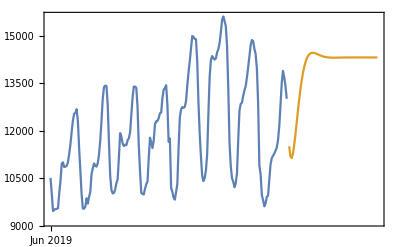

```mathematica
tsmodelDLP=DateListPlot[{
	TimeSeriesWindow[
	resampledNEISOLoad,
	{DateObject[{2019,6,1}],
	DateObject[{2019,6,8}]}],loadTSModelforecast}]
```

#### TimeSeriesForecast specifying SARIMA with Automatic Options

```mathematica
tsmodelSARIMA=TimeSeriesModelFit[resampledNEISOLoad,{"SARIMA",{Automatic,Automatic,Automatic}}]
```

TimeSeriesModel[…]

```mathematica
loadTSModelforecastSARIMA=TimeSeriesForecast[tsmodelSARIMA,{72}]
```

TemporalData[…]

```mathematica
tsmodelDLPSARIMA=DateListPlot[{
	TimeSeriesWindow[
	resampledNEISOLoad,
	{DateObject[{2019,6,1}],
	DateObject[{2019,6,8}]}],loadTSModelforecastSARIMA}]
```

-Graphics-

#### TimeSeriesForecast specifying SARIMA with Specified Options

```mathematica
tsmodelSARIMASpecified=TimeSeriesModelFit[resampledNEISOLoad,{"SARIMA",{{1,1,1},{1,1,1},24}}]
```

TimeSeriesModel[…]

```mathematica
loadTSModelforecastSARIMASpecified=TimeSeriesForecast[tsmodelSARIMASpecified,{72}]
```

TemporalData[…]

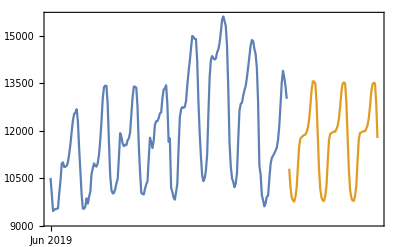

```mathematica
tsmodelDLPSARIMASpecified=DateListPlot[{
	TimeSeriesWindow[
	resampledNEISOLoad,
	{DateObject[{2019,6,1}],
	DateObject[{2019,6,8}]}],loadTSModelforecastSARIMASpecified}]
```